Expresiones y su estructura

Se ha visto ya una gran diversidad del material contenido en Wolfram Language: listas, gráficos, funciones puras y muchas cosas más. Se está ahora en posición de comenzar a tratar con una cuestión fundamental en Wolfram Language: el hecho de que cada una de esas cosas —y, de hecho, todo aquello con lo que trata el lenguaje— está construida siempre en la misma forma básica. Todo ello es lo que se llama una expresión simbólica.

Las expresiones simbólicas son una manera muy general de representar una estructura, potencialmente con un significado asociado a esa estructura. f[x,y] es un ejemplo sencillo de expresión simbólica. Por sí misma, esta expresión simbólica no tiene asociado ningún significado en particular de modo que, al escribirla, Wolfram Language la regresará tal cual, sin cambios.

f[x,y] es una expresión simbólica sin ningún significado particular asociado:

```mathematica
f[x,y]
```

f[x,y]

{x,y,z} es otra expresión simbólica. Aunque internamente es List[x,y,z], se visualiza como {x,y,z}.

La expresión simbólica List[x,y,z] se visualiza como {x,y,z}:

```mathematica
List[x,y,z]
```

{x,y,z}

Frecuentemente, las expresiones simbólicas están anidadas:

```mathematica
List[List[a,b],List[c,d]]
```

{{a,b},{c,d}}

FullForm muestra la forma interna de cualquier expresión simbólica.

```mathematica
FullForm[{{a,b},{c,d}}]
```

List[List[a,b],List[c,d]]

Graphics[Circle[{0,0}]] es otra expresión simbólica, que se muestra en pantalla como la imagen de un círculo. FullForm muestra su estructura interna.

Esta expresión simbólica se visualiza como un círculo:

```mathematica
Graphics[Circle[{0,0}]]
```

-Graphics-

FullForm muestra la estructura subyacente de esa expresión simbólica:

```mathematica
FullForm[-Graphics-]
```

Graphics[Circle[List[0,0]]]

A menudo sucede que las expresiones simbólicas no solo se muestran en pantalla de una manera especial, sino que, además, se evalúan y producen resultados.

Una expresión simbólica que se evalúa para producir un resultado:

```mathematica
Plus[2,2]
```

4

Los elementos de la lista se evalúan, pero la lista misma sigue siendo simbólica:

```mathematica
{Plus[3,3],Times[3,3],Power[3,3]}
```

{6,9,27}

He aquí la estructura de la lista como expresión simbólica:

```mathematica
{Plus[3,3],Times[3,3],Power[3,3]}//FullForm
```

List[6,9,27]

Esto es una expresión simbólica que, además, se evalúa:

```mathematica
Blur[-Graphics-,5]
```

-Graphics-

Lo anterior podría escribirse de este modo:

```mathematica
Blur[Graphics[Circle[{0,0}]],5]
```

-Graphics-

¿Cuáles son los elementos constitutivos más elementales en las expresiones simbólicas? Se les llama átomos (por analogía con los elementos constitutivos básicos de los materiales físicos). Los principales tipos de átomos son los números, las cadenas de caracteres y los símbolos.

Por ejemplo, x, y, f, Plus, Graphics y Table, son símbolos. Todo símbolo tiene un nombre único. En ocasiones, también lleva asociado un significado. A veces, también estará asociado con una evaluación. Y también puede ser parte de la definición de una estructura que usarán otras funciones. Pero no es necesario que sea nada de eso; simplemente debe tener un nombre.

Una característica crucial de Wolfram Language es que puede manejar símbolos puramente como tales, como símbolos (“simbólicamente”), sin que se tengan que evaluar, para producir números, por ejemplo.

En Wolfram Language, x puede simplemente ser x, sin que tenga que evaluarse como alguna otra cosa:

```mathematica
x
```

x

x no se evalúa, pero la suma se hace de todos modos, según las leyes del álgebra, en este caso:

```mathematica
x+x+x+2y+y+x
```

4 x+3 y

Dados símbolos tales como x, y y f, se puede construir una infinidad de expresiones con ellos. Así, f[x], y f[y], y f[x,y]. Y también f[f[x]] o f[x,f[x,y]], o, para el caso, x[x][y,f[x]] o lo que sea.

En general, toda expresión corresponde a un árbol, cuyas “hojas” últimas son átomos. Una expresión puede mostrarse en forma de árbol usando TreeForm.

Una expresión exhibida en forma de árbol:

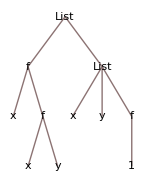

```mathematica
TreeForm[{f[x,f[x,y]],{x,y,f[1]}}]
```

Aquí se tiene una expresión sobre gráficos mostrada en forma de árbol:

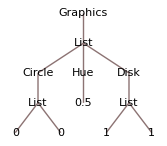

```mathematica
TreeForm[Graphics[{Circle[{0,0}],Hue[0.5],Disk[{1,1}]}]]
```

A fin de cuentas, las expresiones tienen una estructura muy uniforme, así que las operaciones en Wolfram Language operan sobre ellas también de manera muy uniforme.

Por ejemplo, cualquier expresión tiene partes, como las de una lista, que se pueden extraer mediante el uso de [[...]].

Esto es equivalente a {x,y,z}[[2]], y extrae el segundo elemento de una lista:

```mathematica
List[x,y,z][[2]]
```

y

La extracción de partes funciona de igual forma en la siguiente expresión:

```mathematica
f[x,y,z][[2]]
```

y

Esto extrae el círculo del gráfico:

```mathematica
Graphics[Circle[{0,0}]][[1]]
```

Circle[{0,0}]

Y, de igual modo, se extraen a continuación las coordenadas de su centro:

```mathematica
Graphics[Circle[{0,0}]][[1,1]]
```

{0,0}

Esto llega exactamente al mismo resultado:

```mathematica
-Graphics-[[1,1]]
```

{0,0}

En f[x,y], a f se le llama encabezado de la expresión. x y y se llaman argumentos. La función Head extrae el encabezado de una expresión.

El encabezado de una lista es List:

```mathematica
Head[{x,y,z}]
```

List

Toda parte de una expresión tiene un encabezado, incluyendo sus átomos.

El encabezado de un entero es Integer:

```mathematica
Head[1234]
```

Integer

El encabezado de un número real aproximado es Real:

```mathematica
Head[12.45]
```

Real

El encabezado de una cadena de caracteres es String:

```mathematica
Head["hello"]
```

String

Hasta los símbolos tienen un encabezado, a saber: Symbol.

```mathematica
Head[x]
```

Symbol

Mediante el uso de los patrones se pueden buscar coincidencias de expresiones con encabezados dados. _Integer representa cualquier entero, _String cualquier cadena de caracteres y así sucesivamente.

_Integer es un patrón que coincide únicamente con objetos que tengan el encabezado Integer:

```mathematica
Cases[{x,y,3,4,z,6,7},_Integer]
```

{3,4,6,7}

Los patrones denominados pueden también tener encabezados especificados:

```mathematica
Cases[{99,x,y,z,101,102},n_Integer->{n,n}]
```

{{99,99},{101,101},{102,102}}

Al usar Wolfram Language, la mayor parte de los encabezados que se ven son símbolos. Sin embargo, hay casos importantes donde aparecen encabezados más complicados. Uno de estos casos es el de las funciones puras, donde al aplicar una función pura dicha función pura aparece como encabezado.

He aquí la forma completa de una función pura (# es Slot[1]):

```mathematica
FullForm[#^2&]
```

Function[Power[Slot[1],2]]

Al aplicar la función pura, esta aparece como encabezado:

```mathematica
Function[Power[Slot[1],2]] [1000]
```

1000000

A medida que uno se vuelve más sofisticado en la programación en Wolfram Language, se van encontrando cada vez más casos de encabezados complicados. De hecho, muchas de las funciones que se han revisado hasta ahora tienen formas de operador, donde aparecen como encabezados; y, el usarlas de esta forma, lleva a estilos de programación muy poderosos y elegantes.

Select aparece aquí como encabezado:

```mathematica
Select[#>4&][{1,2.2,3,4.5,5,6,7.5,8}]
```

{4.5,5,6,7.5,8}

Tanto Cases como Select aparecen como encabezados en este ejemplo:

```mathematica
Cases[_Integer]@Select[#>4&]@{1,2.2,3,4.5,5,6,7.5,8}
```

{5,6,8}

Todas las operaciones estructurales básicas para listas que se han visto trabajan exactamente igual en el caso de expresiones arbitrarias.

Length no pone atención en cuál sea el encabezado de una expresión; simplemente cuenta los argumentos:

```mathematica
Length[f[x,y,z]]
```

3

/@ tampoco pone atención en cuál sea el encabezado de una expresión; simplemente aplica una función a sus argumentos:

```mathematica
f/@g[x,y,z]
```

g[f[x],f[y],f[z]]

Dado que hay muchas funciones que generan listas, resulta conveniente construir estructuras en forma de listas, aun si al final hay que sustituir las listas por otras funciones.

@@ sustituye el encabezado de la lista por f:

```mathematica
f@@{x,y,z}
```

f[x,y,z]

Esto da Plus[1,1,1,1], lo que entonces se evalúa:

```mathematica
Plus@@{1,1,1,1}
```

4

Esto convierte una lista en una regla:

```mathematica
#1->#2&@@{x,y}
```

x→y

Aquí se ve una alternativa más sencilla, sin hacer explícita la función pura:

```mathematica
Rule@@{x,y}
```

x→y

Una situación insospechadamente común se da cuando se tiene una lista de listas, donde se quiere sustituir las listas interiores por alguna función. Eso puede efectuarse con @@ y /@. Sin embargo, @@@ es una forma directa y más conveniente para ese propósito.

Sustituya las listas interiores por f:

```mathematica
f@@@{{1,2,3},{4,5,6}}
```

{f[1,2,3],f[4,5,6]}

Convierta en reglas las listas interiores:

```mathematica
Rule@@@{{1,10},{2,20},{3,30}}
```

{1→10,2→20,3→30}

He aquí un ejemplo de cómo se puede utilizar @@@ para construir un grafo a partir de una lista de parejas.

Esto genera una lista de parejas de caracteres:

```mathematica
Partition[Characters["antidisestablishmentarianism"],2,1]
```

{{a,n},{n,t},{t,i},{i,d},{d,i},{i,s},{s,e},{e,s},{s,t},{t,a},{a,b},{b,l},{l,i},{i,s},{s,h},{h,m},{m,e},{e,n},{n,t},{t,a},{a,r},{r,i},{i,a},{a,n},{n,i},{i,s},{s,m}}

Convierta lo anterior en una lista de reglas:

```mathematica
Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1]
```

{a→n,n→t,t→i,i→d,d→i,i→s,s→e,e→s,s→t,t→a,a→b,b→l,l→i,i→s,s→h,h→m,m→e,e→n,n→t,t→a,a→r,r→i,i→a,a→n,n→i,i→s,s→m}

Forme un gráfico de transiciones que muestre cómo cada letra es la sucesiva de cada otra:

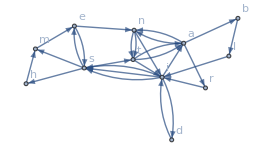

```mathematica
Graph[Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1],VertexLabels->All]
```

Vocabulario

FullForm[expr] |   | muestra la forma interna completa 
TreeForm[expr] |   | muestra la estructura de árbol 
Head[expr] |   | extrae el encabezado de una expresión 
_encabezado |   | busca la coincidencia de una expresión con un encabezado particular
f@@lista |   | sustituye el encabezado de lista con f
f@@@{lista_1,lista_2, ...} |   | sustituye los encabezados de lista_1, lista_2, ... con f

"8 Exercises Available" | "Get Started »"

Encuentre el encabezado de la salida de un ListPlot. »

| Expected output: |  
  | Graphics |

Use @@ para calcular el resultado de multiplicar todos los enteros hasta el 100. »

| Expected output: |  
  | 93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000 |

Use @@@ y Tuples para generar {f[a,a],f[a,b],f[b,a],f[b,b]}. »

| Expected output: |  
  | {f[a,a],f[a,b],f[b,a],f[b,b]} |

Haga una lista con las formas de árbol de 4 aplicaciones sucesivas de #^#& comenzando con x. »

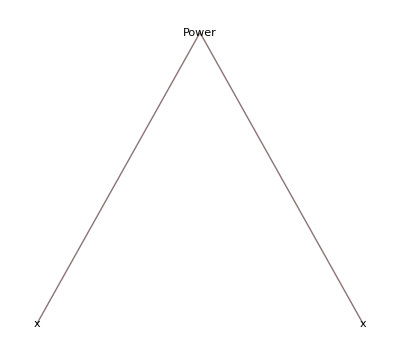
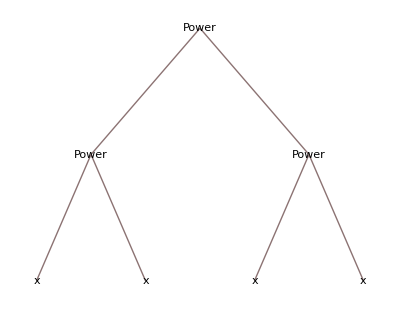
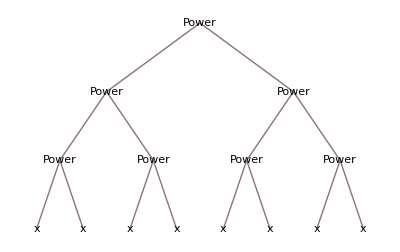
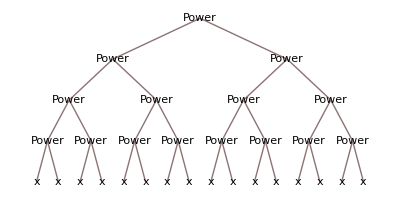
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Encuentre los casos, sin repeticiones, para los que i^2/(j^2+1) es un entero, donde i y j toman valores hasta el 20. »

| Expected output: |  
  | {2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200} |

Cree un grafo que conecte parejas sucesivas de números en Table[Mod[n^2+n,100],{n,100}]. »

| Expected output: |  
  | -Graphics- |

Genere un grafo que muestre qué palabra sigue a cuál en las 200 primeras palabras del artículo en Wikipedia sobre “computers”. »

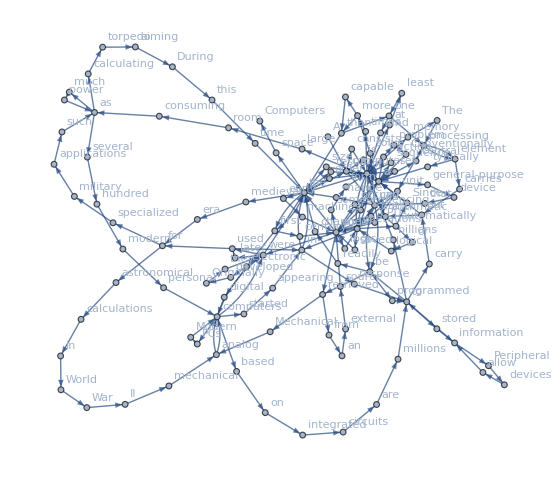
| Sample expected output: |  
  | -Graphics- |

Encuentre una forma más simple para f@@#&/@{{1,2},{7,2},{5,4}}. »

| Sample expected output: |  
  | {f[1,2],f[7,2],f[5,4]} |

Preguntas y respuestas

¿Cómo se interpretan @@ y @@@?

f@@expr es Apply[f,expr]. f@@@expr es Apply[f,expr,{1}]. Por lo general, se leen como “doble arroba” y “triple arroba”.

¿Son árboles todas las expresiones en Wolfram Language?

En un nivel estructural, sí. Sin embargo, cuando se tienen variables con valores asignados (ver la Sección 38), se comportan más bien como grafos dirigidos. Y, por supuesto, se puede usar Graph para representar cualquier grafo como una expresión en Wolfram Language.

Notas técnicas

El concepto básico de los lenguajes simbólicos procede directamente de los trabajos sobre lógica matemática, que se remontan a los años 1930 y anteriores pero, aparte de Wolfram Language, son muy raros los que lo han implementado en la práctica.

Las expresiones en Wolfram Language se parecen un poco a las de XML (y se pueden convertir de unas a otras). Pero, a diferencia de las expresiones en XML, las de Wolfram Language pueden evaluarse, de tal modo que cambien su estructura automáticamente.

Cosas como Select[f], que se han establecido para aplicarse a expresiones, se llaman formas de operador, por analogía con los operadores en matemáticas. El usar Select[f][expr] en vez de Select[expr,f] se llama generalmente currificación, por el especialista en lógica Haskell Curry.

Los símbolos como x pueden usarse para representar variables algebraicas o “incógnitas”. Esto es de importancia central para hacer cosas muy diversas en matemáticas con Wolfram Language.

LeafCount da el número total de átomos en las hojas de un árbol de expresión. ByteCount da el número de bytes necesarios para almacenar dicha expresión.

Para explorar más

Guía para expresiones en Wolfram Language »